## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/andes/LogProcessing/self-improved-tutor

```mathematica
journalStyle={FontSize->9 (* ACM default font for text (10 for large journal format) *)};
figureWidth=72 If[False,6.5 (* Maximum allowed width for ACM journal large format. *),
	10/3 (* ACM journal column with for two-column format. *)];
```

```mathematica
data=Import["guerra-summer-2012-expectation.csv"];
```

```mathematica
Take[data,5]
```

{{Section,student,KC,condition,prob,gain,gainSquared,L,LSquared},{asu_7e256268bab914fb5asul1_,md5:3f6382444a54a0b87ee01b3eb66502db,draw-vector-aligned-axes,control,0.268941,0,0,0.268941,0.268941},{asu_7e256268bab914fb5asul1_,md5:3f6382444a54a0b87ee01b3eb66502db,draw-vector-aligned-axes,mlh,0,0,0,0,0},{asu_7e256268bab914fb5asul1_,md5:b5a232d14b85a64078d32c873932fe4c,draw-vector-aligned-axes,control,0.51825,0,0,1.81388,6.99638},{asu_7e256268bab914fb5asul1_,md5:b5a232d14b85a64078d32c873932fe4c,draw-vector-aligned-axes,mlh,0.129563,0,0,0.129563,0.129563}}

Need to group into KCs, remove header row.

```mathematica
Print[conditions=Union[Map[#[[4]]&,Rest[data]]]];
Length[allKCs=Union[Map[#[[3]]&,Rest[data]]]]
```

{control,mlh}

289

```mathematica
analyzeKC[subdata_]:=Block[{probs=Map[#[[5]]&,subdata],gains=Map[#[[6]]&,subdata],gains2=Map[#[[7]]&,subdata],step=Map[#[[8]]&,subdata],step2=Map[#[[9]]&,subdata]},
(* Make sure there is data for each condition and that the errors can be estimated. *)
If[0<Total[probs] (*&& Total[step2]*Total[probs]>Total[step]^2 &&  Total[gains2]*Total[probs]>Total[gains]^2*), 
(* learning step averaged over students and associated standard error. *)
{{Total[step]/Total[probs],Sqrt[Total[step2]-Total[step]^2/Total[probs]]/Total[probs]},
(* performance gain averaged over students along with associated standard error. *)
{Total[gains]/Total[probs],Sqrt[Total[gains2]-Total[gains]^2/Total[probs]]/Total[probs]}}]]
```

```mathematica
diffs=Outer[Function[{kc,condition},analyzeKC[Select[Rest[data],(#[[3]]==kc && #[[4]]==condition)&]]],allKCs,conditions]
```

{{{{2.57039,1.09592},{-0.027168,0.113818}},Null},{{{1.14351,0.241471},{-0.605339,0.323758}},{{1.,0.},{0.,0.}}},{Null,Null},{{{1.09334,0.228508},{0.,0.}},{{1.,0.},{-0.666667,0.352722}}},{{{1.50361,0.381246},{-0.0614586,0.0743687}},{{1.52999,0.324547},{-0.099839,0.104843}}},{Null,Null},{{{14.4785,3.27911},{-0.117516,0.119743}},{{16.7087,5.11358},{-0.10945,0.0891549}}},{{{2.35377,1.00675},{-0.309915,0.295513}},{{1.,0.},{0.,0.}}},{{{32.813,7.80883},{-0.194419,0.11675}},{{31.8665,7.77534},{-0.058376,0.0890372}}},{{{12.0164,2.81199},{-0.204389,0.090938}},{{13.8874,3.59293},{-0.102339,0.11223}}},{{{4.08107,1.28353},{-0.0869657,0.0826272}},{{3.87512,0.962539},{-0.0028931,0.0899856}}},{{{1.,0.},{0.,0.}},Null},{{{1.08753,0.181608},{0.,0.}},{{1.08753,0.181608},{-0.245878,0.276719}}},{Null,Null},{{{2.43314,1.28306},{-0.02764,0.065896}},{{1.7096,0.427846},{-0.143379,0.125732}}},{{{1.46105,0.875094},{0.,0.}},{{2.20179,0.787018},{-0.0280827,0.0513503}}},{Null,Null},{{{1.,0.},{0.,0.}},{{1.5,0.767975},{0.,0.}}},{{{1.,6.49233×10^-9},{-0.366858,0.267505}},{{1.,0.},{0.,0.}}},{{{1.30591,0.553596},{0.,0.}},{{1.,0.},{0.,0.}}},{{{9.34655,2.34232},{-0.189926,0.120757}},{{9.68239,2.57411},{-0.146041,0.115247}}},{Null,Null},{{{1.,0.},{-0.424607,0.295157}},{{1.,0.},{-0.262686,0.292323}}},{{{6.59724,1.57753},{-0.0270476,0.0813207}},{{6.62873,1.51339},{-0.107827,0.124373}}},{{{3.09223,0.980352},{-0.326669,0.129156}},{{3.30982,0.896162},{-0.321901,0.147045}}},{{{1.89863,0.52175},{-0.0242784,0.0455307}},{{2.29655,0.567516},{-0.107461,0.0977722}}},{{{3.18002,2.59624},{-0.618002,0.259624}},{{1.89273,1.07519},{-0.835535,0.215731}}},{{{2.05309,0.437519},{-0.367922,0.214459}},{{1.84835,0.500024},{-0.0420159,0.0734014}}},{{{1.69349,0.737778},{-0.082074,0.142585}},{{1.,0.+1.30595×10^-8 ⅈ},{0.,0.}}},{{{1.,0.},{0.,0.}},{{1.,0.+1.30595×10^-8 ⅈ},{0.,0.}}},{{{2.55377,0.90499},{0.,0.}},{{2.,0.460205},{0.,0.}}},{{{6.61666,1.96566},{-0.0811759,0.123617}},{{7.40217,2.02745},{-0.149926,0.134497}}},{{{1.09808,0.176995},{-0.0661584,0.118616}},{{1.43983,0.433465},{-0.0438058,0.0795106}}},{Null,Null},{{{2.5334,0.714943},{-0.191037,0.195196}},{{2.14642,0.444538},{-0.201861,0.204717}}},{{{2.49147,1.08154},{-0.0738725,0.0800683}},{{1.07713,0.160943},{0.,0.}}},{{{1.5,0.767975},{0.,0.}},Null},{{{1.9388,0.519486},{-0.0699379,0.0945808}},{{2.0876,0.449117},{-0.207928,0.209975}}},{{{17.697,3.35426},{-0.104216,0.0819406}},{{16.4525,4.31078},{-0.0623762,0.0757922}}},{{{2.59061,0.905582},{-0.0745821,0.0944509}},{{2.90119,0.604357},{-0.125599,0.098485}}},{{{2.2195,0.557833},{-0.136027,0.102366}},{{1.93059,0.471768},{-0.310016,0.196386}}},{Null,Null},{{{2.80245,0.815562},{-0.409519,0.214338}},{{1.86226,0.432362},{-0.0680247,0.0922231}}},{{{2.52434,0.386486},{-0.572815,0.165887}},{{2.28931,0.466415},{-0.51209,0.201023}}},{{{4.25974,1.21001},{0.00182527,0.121322}},{{3.32409,0.722582},{-0.0934911,0.105632}}},{{{1.65205,0.322954},{0.,0.}},{{1.41212,0.306329},{-0.0536325,0.0962926}}},{Null,Null},{{{6.76047,1.80389},{-0.414695,0.139824}},{{6.50687,1.69298},{-0.31579,0.198354}}},{{{2.05353,0.491811},{-0.219192,0.166138}},{{2.15006,0.381651},{-0.0734554,0.10128}}},{{{1.77201,0.494751},{-0.0727213,0.079113}},{{1.81642,0.473963},{0.,0.}}},{{{1.,7.45951×10^-9},{-0.298052,0.323626}},{{1.,0.},{-0.525372,0.331687}}},{{{2.16764,0.969736},{-0.339421,0.222498}},{{2.6666,0.932928},{-0.342397,0.20952}}},{{{1.49058,0.287468},{0.,0.}},{{1.44444,0.359785},{0.,0.}}},{{{1.,0.},{-0.256186,0.286343}},{{1.2553,0.283234},{-0.287218,0.282222}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},Null},{{{1.,0.+7.36334×10^-9 ⅈ},{0.,0.}},{{1.,0.},{0.,0.}}},{Null,Null},{{{7.26682,1.65001},{-0.270409,0.157376}},{{5.41665,1.74907},{-0.0352855,0.151882}}},{{{1.2,0.459942},{0.,0.}},Null},{{{5.24131,1.80211},{-0.0390531,0.0754582}},{{5.96413,1.73008},{-0.0448315,0.101064}}},{Null,{{1.,0.},{0.,0.}}},{{{2.85297,0.62843},{0.0173909,0.039029}},{{1.83979,0.826081},{0.0165108,0.0515333}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.82602,0.4304},{-0.349445,0.176962}},{{1.68711,0.396474},{-0.0513741,0.0932359}}},{{{373.153,94.8515},{-0.0473911,0.051603}},{{354.386,115.357},{0.0565496,0.0580155}}},{Null,Null},{{{1.91396,0.371549},{-0.110772,0.0874929}},{{2.38941,0.518393},{-0.406604,0.171423}}},{Null,Null},{Null,{{1.,0.},{0.,0.}}},{{{1.37455,0.547716},{0.,0.}},{{1.,0.},{0.,0.}}},{{{5.79692,1.27999},{-0.306327,0.160101}},{{5.41855,1.16052},{-0.26916,0.127353}}},{Null,Null},{Null,Null},{Null,Null},{{{1.12133,0.216117},{-0.0606655,0.108058}},{{1.,0.},{0.,0.}}},{Null,Null},{Null,Null},{{{1.31084,0.270804},{-0.228231,0.201904}},{{1.5,0.268483},{-0.276121,0.207305}}},{{{1.,0.},{0.,0.}},Null},{{{3.83894,0.919532},{-0.200896,0.116803}},{{4.91627,1.14035},{-0.0169781,0.0655453}}},{{{5.55878,1.07258},{-0.349948,0.13652}},{{4.71831,1.55652},{-0.22018,0.127698}}},{Null,Null},{Null,Null},{{{2.19885,0.492357},{-0.0889832,0.0842099}},{{2.37243,0.684447},{-0.0854386,0.10612}}},{{{3.32192,0.819702},{-0.144139,0.122036}},{{2.93417,0.623209},{-0.0773527,0.0637772}}},{Null,{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},{{1.,0.},{-1.,0.}}},{{{30.2757,7.23182},{-0.203939,0.129357}},{{37.4838,8.987},{-0.271458,0.146021}}},{{{1.,0.},{0.,0.}},Null},{{{1.68551,0.430672},{-0.192592,0.14943}},{{2.22393,0.580411},{-0.283576,0.201622}}},{{{10.2275,2.01627},{-0.280244,0.120927}},{{13.6193,3.27375},{-0.41344,0.181233}}},{{{2.,0.508456},{0.,0.}},Null},{{{1.87877,0.57537},{-0.482369,0.235857}},{{1.67394,0.349772},{-0.340481,0.239903}}},{{{2.87931,0.52279},{-0.262503,0.158456}},{{2.93244,0.697443},{-0.367569,0.127169}}},{{{1.,0.},{0.,0.}},Null},{{{3.21531,0.973819},{-0.149137,0.132695}},{{2.64755,0.902585},{-0.0602711,0.0828825}}},{{{1.39214,0.437259},{-0.11107,0.186145}},Null},{Null,Null},{Null,Null},{Null,Null},{Null,Null},{{{1.14141,0.227285},{-0.553669,0.264849}},{{1.05927,0.147806},{-0.703652,0.285841}}},{{{1.,0.},{0.,0.}},Null},{{{1.99024,0.765166},{0.,0.}},{{1.72605,0.464285},{0.,0.}}},{{{3.17784,0.681741},{-0.43222,0.137305}},{{3.43605,0.664132},{-0.362216,0.14956}}},{Null,Null},{{{1.18064,0.233854},{-0.271155,0.252131}},{{1.23807,0.297207},{-0.067431,0.119181}}},{Null,Null},{Null,Null},{{{1.73788,0.406821},{-0.559832,0.236603}},{{1.37383,0.366409},{-0.115092,0.119578}}},{{{3.24529,1.07205},{-0.010816,0.0489727}},{{2.86142,0.682809},{-0.0633133,0.0840468}}},{{{1.72643,0.483945},{0.,0.}},{{1.68027,0.407976},{-0.0506633,0.0702182}}},{{{1.78586,0.848314},{0.0125965,0.042087}},{{1.18178,0.25549},{0.,0.}}},{{{4.25405,1.24622},{-0.10199,0.13192}},{{3.9538,1.00539},{-0.0289907,0.0497848}}},{Null,Null},{{{3.14954,1.23668},{-0.138651,0.146681}},{{1.5,0.292888},{-0.281085,0.23819}}},{{{1.,0.},{0.,0.}},Null},{{{1.,0.},{0.,0.}},Null},{{{1.45707,0.449275},{-0.253487,0.259508}},{{1.90151,0.62318},{-0.115806,0.150039}}},{{{1.59015,0.485706},{-0.66392,0.426209}},{{1.20455,0.302717},{-0.335316,0.354292}}},{Null,Null},{Null,Null},{Null,Null},{Null,Null},{{{1.43609,0.551599},{0.,0.}},Null},{{{5.13855,1.35919},{-0.277017,0.137764}},{{3.18461,0.697986},{-0.450582,0.19042}}},{Null,Null},{{{2.36136,1.00465},{0.,0.}},Null},{{{1.87961,0.738643},{-0.248975,0.279629}},{{1.,0.},{0.,0.}}},{{{1.36657,0.490826},{-0.117012,0.148194}},{{2.21779,1.04762},{0.,0.}}},{{{1.53653,0.288397},{-0.202381,0.232362}},{{1.3685,0.284465},{-0.0263004,0.0658199}}},{{{2.1323,0.714181},{-0.0964222,0.11696}},{{2.5029,1.30639},{0.,0.}}},{{{4.91724,1.23182},{-0.201632,0.124281}},{{5.82484,1.6193},{-0.171926,0.173849}}},{{{2.39936,0.722439},{-0.281632,0.178384}},{{2.45562,0.672427},{-0.124765,0.116057}}},{Null,Null},{Null,Null},{{{1.18839,0.260685},{0.,0.}},{{1.17221,0.34034},{0.,0.}}},{{{6.55156,1.4991},{-0.154907,0.150074}},{{8.9908,2.17998},{-0.219517,0.13022}}},{{{3.26244,0.887528},{-0.0272501,0.061442}},{{3.07628,0.779143},{-0.158882,0.118148}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{10.5312,2.47554},{-0.268137,0.126589}},{{12.7801,2.31444},{-0.362915,0.13846}}},{{{4.79195,1.10682},{-0.101411,0.10871}},{{5.17165,1.29889},{-0.00649848,0.0164643}}},{{{2.41668,0.554051},{-0.105985,0.125724}},{{2.57429,0.770032},{-0.19145,0.18532}}},{{{4.42808,1.04032},{-0.468367,0.131424}},{{5.56165,0.932425},{-0.389484,0.135271}}},{{{1.38708,0.389584},{0.,0.}},{{1.17221,0.34034},{0.,0.}}},{{{3.80924,0.912336},{-0.186588,0.0853342}},{{3.28953,0.947573},{-0.0976005,0.127835}}},{{{13.373,3.01845},{0.0476287,0.0872843}},{{15.2965,3.36429},{-0.193278,0.142036}}},{{{1.37772,0.592045},{-0.428658,0.419912}},Null},{{{8.47799,2.25046},{-0.106082,0.146458}},{{8.76707,2.43128},{-0.12762,0.128696}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.39602,0.335858},{-0.215119,0.24699}},{{1.,0.},{0.,0.}}},{{{1.13077,0.16998},{0.,0.}},{{1.20337,0.339639},{0.,0.}}},{{{250.785,79.663},{0.0789772,0.0426563}},{{318.436,92.8311},{0.0717159,0.0192793}}},{{{1.,0.},{0.,0.}},Null},{Null,Null},{{{2.45279,0.483924},{-0.298525,0.193773}},{{1.91754,0.541949},{-0.103638,0.138151}}},{{{2.86328,0.885686},{-0.452551,0.207811}},{{1.98447,0.484724},{-0.189357,0.142991}}},{Null,Null},{{{1.5,0.505651},{-0.14162,0.227832}},{{1.5,0.671829},{-0.25,0.335915}}},{Null,Null},{{{1.2,0.459942},{-0.9,0.229971}},Null},{{{2.28361,0.463622},{-0.423701,0.216738}},{{2.,0.442207},{-0.185468,0.19023}}},{Null,Null},{{{1.,0.},{0.,0.}},Null},{{{1.49653,0.47614},{0.,0.}},{{1.57236,0.279385},{-0.0883181,0.10768}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{151.471,44.1333},{-0.00771849,0.0810882}},{{187.684,47.9703},{0.0319043,0.0746235}}},{Null,Null},{{{1.,0.},{-0.20394,0.235816}},{{1.,0.},{-0.344422,0.361412}}},{Null,{{1.,0.},{0.,0.}}},{{{1.62951,0.368804},{-0.18549,0.187517}},{{1.53453,0.343208},{-0.0403775,0.0735628}}},{{{1.32614,0.484816},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},Null},{{{1.73833,0.404821},{-0.341589,0.202639}},{{1.63108,0.472174},{-0.180899,0.168417}}},{Null,Null},{{{1.,0.+6.60943×10^-9 ⅈ},{-0.746949,0.24348}},{{1.,0.},{-0.256186,0.286343}}},{{{1.,0.+6.60943×10^-9 ⅈ},{0.,0.}},{{1.,0.},{0.,0.}}},{Null,{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{2.26846,0.499943},{-0.33125,0.174287}},{{2.22891,0.813936},{-0.573619,0.233358}}},{{{1.24271,0.35046},{0.,0.}},{{1.29137,0.271355},{-0.242756,0.24647}}},{Null,Null},{{{1.39214,0.437259},{-0.11107,0.186145}},Null},{Null,Null},{{{1.5,0.671829},{-0.25,0.335915}},Null},{Null,Null},{Null,Null},{{{3.5323,0.93759},{-0.128718,0.129545}},{{3.72012,0.763576},{-0.165486,0.136893}}},{{{1.,0.},{-0.424607,0.417416}},{{1.05004,0.125402},{0.,0.}}},{{{1.54874,0.434717},{-0.258982,0.223376}},{{1.59488,0.609497},{-0.102765,0.174056}}},{{{1.27228,0.443887},{0.,0.}},{{2.0207,0.549334},{-0.267321,0.273901}}},{{{2.,1.1031},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.89708,0.340138},{-0.396588,0.185813}},{{1.31492,0.330926},{-0.242548,0.230559}}},{{{1.97639,0.807103},{-0.509627,0.390439}},{{1.,0.},{-0.407879,0.406758}}},{{{2.93187,0.841011},{-0.302427,0.186435}},{{2.40168,0.671826},{-0.257483,0.196472}}},{{{1.19599,0.251335},{-0.532875,0.29776}},{{1.,0.},{-0.553196,0.479222}}},{{{1.44073,0.715942},{0.,0.}},{{1.,0.+2.48576×10^-8 ⅈ},{0.,0.}}},{Null,Null},{{{1.20353,0.345155},{-0.101764,0.172578}},{{1.19643,0.226365},{-0.414263,0.273472}}},{Null,Null},{Null,Null},{{{1.,1.02541×10^-8},{-0.289712,0.316434}},{{1.,0.},{-0.688845,0.352123}}},{{{2.22339,0.547282},{0.,0.}},{{1.,0.},{0.,0.}}},{{{3.07227,1.09433},{-0.185586,0.152948}},{{2.54977,0.735652},{-0.281157,0.263556}}},{{{2.,1.1031},{0.,0.}},Null},{{{1.76807,0.471002},{-0.0369721,0.0676078}},{{2.08882,0.422926},{-0.109634,0.106277}}},{{{1.46133,0.267335},{-0.195764,0.205307}},{{1.53342,0.267644},{-0.200944,0.181509}}},{{{2.21737,0.493281},{-0.257017,0.15362}},{{2.05372,0.922817},{-0.26666,0.230477}}},{{{1.,0.},{0.,0.}},Null},{Null,Null},{{{1.,0.},{0.,0.}},Null},{{{1.30729,0.311468},{-0.169739,0.169977}},{{1.83008,0.430784},{-0.135163,0.131628}}},{{{2.15448,0.776947},{-0.240149,0.236847}},{{2.07462,0.533004},{-0.110507,0.102328}}},{{{4.32097,0.914332},{-0.127264,0.092363}},{{3.43542,0.895197},{0.0287234,0.0702284}}},{{{2.82306,1.02597},{-0.206733,0.233599}},{{3.24675,0.922435},{-0.0313829,0.0850401}}},{{{1.11606,0.237025},{0.,0.}},{{1.28087,0.263507},{-0.20468,0.236562}}},{Null,Null},{Null,Null},{Null,Null},{{{1.,0.},{0.,0.}},Null},{Null,Null},{Null,Null},{Null,Null},{{{1.,0.},{0.,0.}},{{1.,0.},{-0.688845,0.497977}}},{{{4.90289,1.15383},{-0.108445,0.107365}},{{3.54733,0.812297},{0.0392036,0.0742136}}},{{{110.627,28.2137},{0.0329624,0.0661452}},{{130.897,34.0056},{0.0351714,0.0720592}}},{Null,Null},{{{3.34705,1.04792},{-0.373246,0.162593}},{{2.82135,0.869146},{-0.509589,0.199016}}},{{{1.35915,0.411199},{-0.539121,0.38101}},{{1.,0.},{0.,0.}}},{{{1.50153,0.458741},{-0.447668,0.219425}},{{2.05042,0.412019},{-0.470258,0.262681}}},{{{3.9237,1.37002},{-0.109177,0.111908}},{{3.27011,0.864564},{-0.184092,0.15301}}},{{{2.75565,0.696247},{-0.131069,0.0791859}},{{2.12862,0.682199},{2.80566×10^-18,0.0210947}}},{{{1.53475,0.540403},{-0.0748993,0.131233}},{{1.14351,0.241471},{-0.322904,0.308553}}},{Null,{{1.,0.},{0.,0.}}},{{{3.50185,1.07419},{-0.24701,0.181138}},{{3.63045,0.883579},{-0.179952,0.114016}}},{{{1.44637,0.470359},{-0.107686,0.138264}},{{1.,0.},{0.,0.}}},{{{2.89541,0.85202},{-0.158197,0.126061}},{{4.09908,1.36303},{-0.216915,0.185566}}},{{{1.5,0.767975},{0.,0.}},Null},{{{4.73071,1.04397},{-0.26574,0.151593}},{{4.45765,0.938189},{-0.283765,0.129381}}},{Null,Null},{{{6.9504,1.95204},{-0.0922287,0.106973}},{{7.16602,1.73573},{-0.100745,0.130858}}},{{{1.,0.},{0.,0.}},{{1.52659,0.438406},{-0.594831,0.322684}}},{Null,Null},{Null,Null},{{{3.,0.627226},{-0.937204,0.124471}},{{1.78825,0.715609},{0.,0.}}},{{{1.,0.},{0.,0.}},{{1.,0.},{-1.,0.}}},{{{4.70981,1.08247},{-0.0463843,0.093056}},{{6.4861,1.60572},{-0.342923,0.151732}}},{Null,Null},{{{3.30403,0.831497},{0.0105,0.0415924}},{{1.71263,0.43456},{-0.0699376,0.101313}}},{{{1.,0.},{0.,0.}},Null},{Null,Null},{Null,Null},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.,7.45951×10^-9},{-0.298052,0.323626}},{{1.10854,0.194739},{-0.287621,0.263949}}},{Null,Null},{{{1.,0.},{-1.,0.}},{{1.,0.},{0.,0.}}},{Null,Null},{{{1.,0.},{0.,0.}},Null},{{{2.42501,0.906267},{-0.0559546,0.07515}},{{2.89417,0.984313},{-0.383418,0.194124}}},{{{1.5,0.671829},{-0.25,0.335915}},{{1.,0.},{0.,0.}}},{{{1.91536,0.468048},{-0.0658875,0.0895733}},{{2.07641,0.379619},{-0.267012,0.200328}}},{{{1.5,0.767975},{0.,0.}},Null},{{{3.30219,1.30779},{-0.0540979,0.0600302}},{{4.29073,1.66219},{0.0173018,0.0649731}}},{{{1.37666,0.258862},{-0.328012,0.200874}},{{1.63344,0.353971},{-0.201066,0.156603}}},{{{1.06894,0.14449},{0.,0.}},{{1.,7.45951×10^-9},{0.,0.}}},{{{1.19131,0.226854},{0.,0.}},{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},Null},{{{1.12678,0.257347},{0.,0.}},{{1.,0.+2.48576×10^-8 ⅈ},{0.,0.}}},{{{1.45886,0.329249},{-0.279071,0.163407}},{{1.83414,0.426031},{-0.08355,0.104006}}},{{{3.61472,1.07614},{-0.244479,0.220393}},{{2.65796,0.929016},{-0.378973,0.239697}}},{{{2.83858,0.708106},{-0.160942,0.143694}},{{2.92792,0.793334},{-0.0571375,0.0967771}}},{Null,Null},{Null,Null},{Null,Null},{Null,Null},{{{1.,0.},{0.,0.}},Null},{Null,Null},{Null,Null},{{{2.33825,0.791383},{0.0159955,0.0330082}},{{2.07326,0.672414},{-0.0855995,0.122341}}},{{{1.51991,0.481492},{-0.070083,0.105187}},{{1.32511,0.313444},{-0.421304,0.250926}}},{{{1.,0.},{0.,0.}},Null},{Null,{{1.,0.},{0.,0.}}},{{{2.46151,0.584665},{-0.0208419,0.0543724}},{{1.90506,0.417828},{-0.431832,0.206688}}},{Null,{{1.,0.},{0.,0.}}},{{{8.1602,2.18189},{-0.113659,0.10331}},{{9.3753,2.49204},{-0.152108,0.124111}}},{Null,Null}}

Scatter plot showing number of steps before mastery for each KC in each experimetal condition.

179

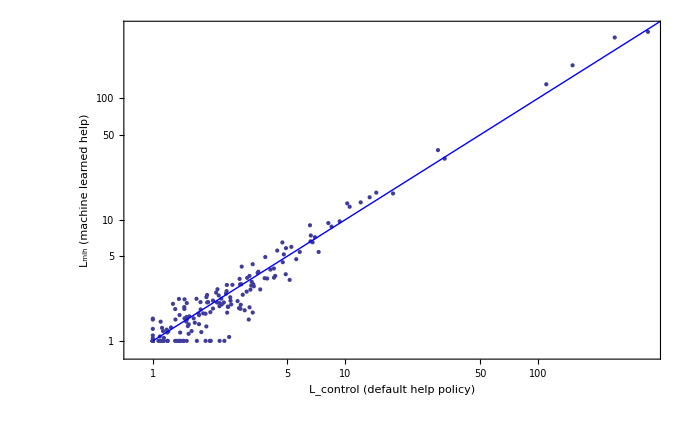

```mathematica
scatterStep=Block[{data=Map[{#[[1,1,1]],#[[2,1,1]]}&,Select[diffs,#[[1]]=!=Null && #[[2]]=!=Null&]]},Print[Length[data]];ListLogLogPlot[data,
(* Seems to be a bug in PlotRange->All, so do this by hand. *) 
PlotRange->{#,#}&[{0.8,Max[Flatten[data]]+10}],Epilog->{Blue,Line[{{0,0},{10,10}}]},Axes->False,Frame->True,FrameLabel->{"L_control (default help policy)","L_mlh (machine learned help)"},BaseStyle->If[True (* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]]
```

```mathematica
.
```

For Presentation, want width 8.5 in = 612 pt and presentation BaseStyle.  Just doing clipboard cut and paste has trouble with some characters.  Graphics using eps in OpenOffice do not render in pdf output.

```mathematica
Export["scatter-step.png",scatterStep,ImageSize->612]
```

scatter-step.png

```mathematica
Export["scatter-step.eps",scatterStep,ImageSize->figureWidth]
```

scatter-step.eps

```mathematica
xx=Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],(* regular mean *) {Mean[val],Sqrt[err.err]/Length[val]},(* maximum likelihood maximizing weighed mean *){val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[2,1,1]]-#[[1,1,1]],Sqrt[#[[1,1,2]]^2+#[[2,1,2]]^2]}&,Select[diffs,#[[1]]=!=Null && #[[2]]=!=Null && Abs[#[[1,1,2]]^2+#[[2,1,2]]^2]>10^-1&]]]]
```

{145,{0.724121,1.44776+0. ⅈ},{-0.10784+0. ⅈ,0.0615629+0. ⅈ}}

This is the  one-tailed p-value from a Z-test

```mathematica
Block[{z=xx[[3,1]]/xx[[3,2]]},(1+Erf[-Abs[z]/Sqrt[2]])/2]
```

0.047348

Select only cases where positive learning was seen in both conditions.  We see that there is almost no difference in the change in number of steps.

```mathematica
xx2=Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],(* regular mean *) {Mean[val],Sqrt[err.err]/Length[val]},(* maximum likelihood maximizing weighed mean *){val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[2,1]]-#[[3,1]],Sqrt[(#[[2,2]])^2+(#[[3,2]])^2]}&,Select[diffs,If[#[[0]]==List , 0<#[[4,1]] && 0<#[[5,1]]]&]]]]
```

{112,{0.688646,1.09809},{-0.0419361,0.0429396}}

```mathematica
<<HypothesisTesting`
```

Scatter plot showing performance gain 1-s-g for each KC in each experimetal condition.

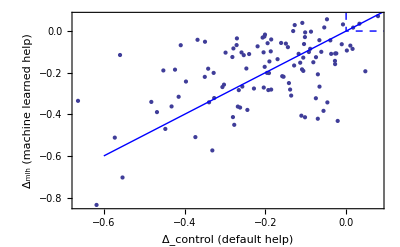

```mathematica
scatterGain=ListPlot[Map[{#[[1,2,1]],#[[2,2,1]]}&,Select[diffs,#[[1]]=!=Null && #[[2]]=!=Null&]],
PlotRange->All,Epilog->{Blue,Line[{{-.6,-.6},{1,1}}],Dashed,Line[{{0,1},{0,0},{1,0}}]},Frame->True,Axes->False,FrameLabel->{"Δ_control (default help policy)","Δ_mlh (machine learned help)"},BaseStyle->If[True (* Choose between journal and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

For Presentation, want width 6.4 in = 460 pt and presentation BaseStyle

```mathematica
Export["scatter-gain.png",scatterGain,ImageSize->460]
```

scatter-gain.png

```mathematica
Export["scatter-gain.eps",scatterGain,ImageSize->figureWidth]
```

scatter-gain.eps

```mathematica
yy=Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],(* regular mean *) {Mean[val],Sqrt[err.err]/Length[val]},(* maximum likelihood maximizing weighed mean *){val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[2,2,1]]-#[[1,2,1]],Sqrt[#[[1,2,2]]^2+#[[2,2,2]]^2]}&,Select[diffs,#[[1]]=!=Null && #[[2]]=!=Null&]]]]
```

{111,{0.00851777,0.0211104},{0.0137376,0.0150329}}

This is the  one-tailed p-value from a Z-test

```mathematica
Block[{z=yy[[3,1]]/yy[[3,2]]},(1+Erf[-Abs[z]/Sqrt[2]])/2]
```

0.180401